# Little Tests

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{NotebookDirectory[],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedInitialSign"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"bamboo_1","0001",r,"clean"];

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=170/r;
ny=300/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io}
ImageDimensions[#]&/@{ia,ib,id,io}

max=MinMax[Flatten[ImageData[id]]][[2]];
Print["max dv=", max]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45},{103,45}}

max dv=12.5952

## Little Tests

#### Little Functions

```mathematica
pyrfi[ia_,ib_,row_,lvlmax_]:=Block[{pyrfia,pyrfib},
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ib][[row]],lvlmax];

Flatten[{pyrfia,pyrfib},{{2},{1},{3}}]
]
```

```mathematica
row=20;
lvlmin=1;
lvlmax=4;

pyrfiab=pyrfi[ia,ib,row,lvlmax];
```

#### Little Test: All packages

```mathematica
row=37;

lvlmin=4;
lvlmax=4;
e=0.05;

pyrfiab=pyrfi[ia,ib,row,lvlmax-1];
```

```mathematica
(* Check solution *)
ic=(*move[ia,-dv]*)ib;
```

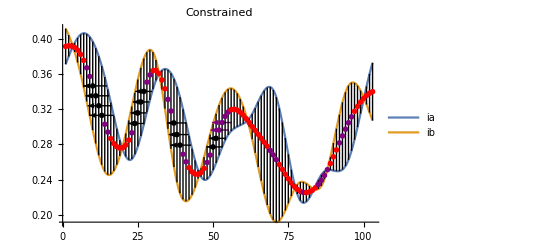

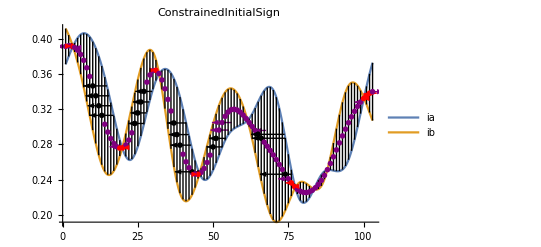

```mathematica
rangex=Range[1,103];

mode="Constrained";
seeAllLine[rangex,pyrfiab[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),mode]
mode="ConstrainedInitialSign";
seeAllLine[rangex,pyrfiab[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),mode]
```

#### Little Test: Initial Value Convergence

```mathematica
p=53;
solution=ImageData[id][[row,p]];
```

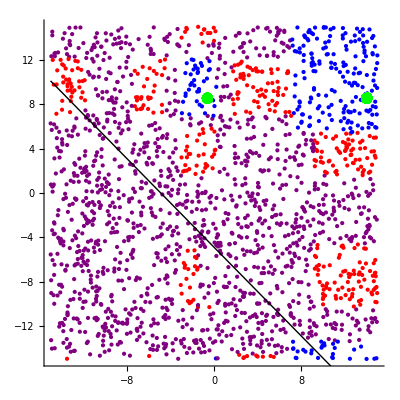

```mathematica
lvlmin=1;
lvlmax=4;
mode="ConstrainedInitialSign";
pixelInitialValueGraphics[10,2000,p,{-15,15},-solution,pyrfiab[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),mode]
```

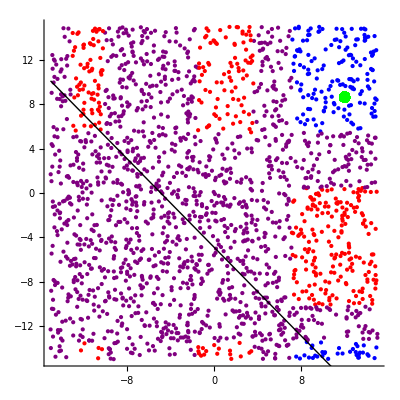

```mathematica
lvlmin=4;
lvlmax=4;
pixelInitialValueGraphics[10,2000,p,{-15,15},-solution,pyrfiab[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),mode]
```

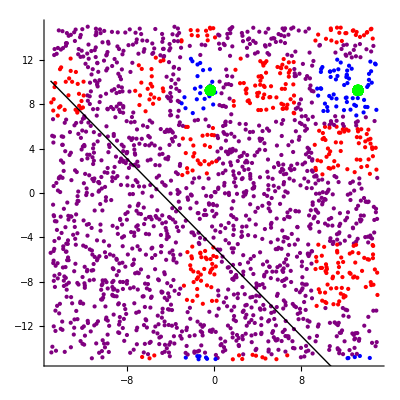

```mathematica
lvlmin=3;
lvlmax=3;
pixelInitialValueGraphics[10,2000,p,{-15,15},-solution,pyrfiab[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),mode]
```

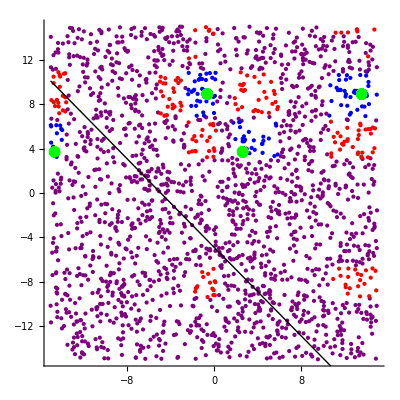

```mathematica
lvlmin=2;
lvlmax=2;
pixelInitialValueGraphics[10,2000,p,{-15,15},-solution,pyrfiab[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),mode]
```

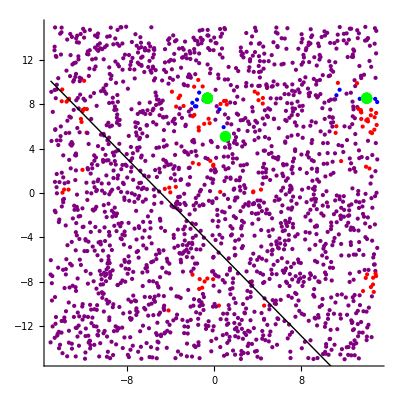

```mathematica
lvlmin=1;
lvlmax=1;
pixelInitialValueGraphics[10,2000,p,{-15,15},-solution,pyrfiab[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),mode]
```

#### Little Test: Animation

```mathematica
lvlmin=1;
lvlmax=1;
(*Last[pixelIterGraphics[10, p,{-11,-0},20, lvlmax,pyrfiab[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"ConstrainedInitialSign"]]*)
```

#### Little Test: See lowest res solution for multiple points and see their initial values for convergence

```mathematica
lvlmin=4;
lvlmax=4;
```

```mathematica
(*
Table[
solution=ImageData[id][[row,p]];
pixelInitialValueGraphics[10,2000,p,{-15,15},-solution,pyrfiab[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"ConstrainedInitialSign"]
,{p,10,103,5}]
*)
```

```mathematica
(*
Table[
solution=ImageData[id][[row,p]];
pixelInitialValueGraphics[10,2000,p,{-15,15},-solution,pyrfiab[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"Constrained"]
,{p,10,103,5}]
*)
```